```mathematica
<<NC`
<<NCAlgebra`
(* <<FiniteFields` *)
```

You are using the version of NCAlgebra which is found in:

/Users/levitt/Documents/NC

You can now use "<< NCAlgebra`" to load NCAlgebra.

```mathematica
NCSetOutput[NonCommutativeMultiply->True]
```

```mathematica
(* Hopf algebras are Coassociative so ⊗ is Flat.
	We implement this carefully to coexist with NonCommutativeMultiply *)
Unprotect[CircleTimes];
     ClearAttributes[CircleTimes, {OneIdentity,Flat}];

    (* Flatten  *)
     CircleTimes[a___, CircleTimes[b__], c___] :=
     CircleTimes[a, b, c]; 

     (* Pull out commutative factors *)
     CircleTimes[a___, b_?CommutativeQ c_, d___] :=
     b CircleTimes[a, c, d];
     CircleTimes[a___, b_?CommutativeQ, c___] :=
     b CircleTimes[a, c]/;b≠1; 

     (* Pull out sums *)
     CircleTimes[a_Plus,b__]:=(CircleTimes[#,b]) &/@ a;
     CircleTimes[a__,b_Plus]:=(CircleTimes[a,#]) &/@ b;

     CircleTimes[a_Symbol] := a;
     CircleTimes[] := 1;
Protect[CircleTimes];
```

```mathematica
(* CircleTimesQ *)
Clear[CircleTimesQ];
  CircleTimesQ[Slot] = False;
  CircleTimesQ[SlotSequence] = False;
  CircleTimesQ[Pattern] = False;
  CircleTimesQ[Blank] = False;
  CircleTimesQ[BlankSequence] = False;
  CircleTimesQ[BlankNullSequence] = False;
CircleTimesQ[x_]:=True/;Head[x]==CircleTimes;
CircleTimesQ[f_[x___]]:=Apply[And, Map[CircleTimesQ,{x}]];
CircleTimesQ[_]:=False;
```

```mathematica
(* Teach NonCommutativeMultiply how to distribute across ⊗'s *)

Unprotect[NonCommutativeMultiply];

NonCommutativeMultiply[a___,b_Plus,c_?CircleTimesQ,d___]:=(NonCommutativeMultiply[a,#,c,d])& /@b;
NonCommutativeMultiply[a___,b_?CircleTimesQ,c_Plus,d___]:=(NonCommutativeMultiply[a,b,#,d])& /@c;

NonCommutativeMultiply[a_?CircleTimesQ , b_?CircleTimesQ,c___]:=
Inner[NonCommutativeMultiply,a,b,CircleTimes]**c /;Length[a]==Length[b]; 

 NonCommutativeMultiply[a_?CircleTimesQ , b_?CircleTimesQ,c___]:=
 Print["Unequal Length Tensors"]/;Length[a]≠Length[b]; 

Protect[NonCommutativeMultiply];
```

```mathematica
(* NCTClean endeavors to take any ⊗ object and then output the ⊗ with it's scalars
	(assumed to be any commutative numbers) as a coefficient out front. *)

(* If given a sum of objects, clean each individually *)
 NCTClean[a_Plus]:=(NCTClean[#]) & /@a; 

(* If given a product of objects, clean each individually
	Stripping out commutative terms first if needed *)
NCTClean[c_?CommutativeQ a_Times]:=c(NCTClean[#]) & /@a; 
NCTClean[a_Times]:=(NCTClean[#]) & /@a;

NCTClean[a_Plus**b__]:=(NCTClean[#**b])&/@a;
 NCTClean[a_**b_Plus]:=(NCTClean[a**#])&/@b; 
NCTClean[a_**b_Plus**c__]:=(NCTClean[a**#**c])&/@b;

NCTClean[a_Times ⊗ b_Times]:=
Catch[Module[{i,aCom=1,aNCom=1,alen=Length[a],bCom=1,bNCom=1,blen=Length[b]},
For[i=1,i≤alen,i++,If[CommutativeQ[a[[i]]],aCom*=a[[i]],aNCom=aNCom**a[[i]]]];
For[i=1,i≤blen,i++,If[CommutativeQ[b[[i]]],bCom*=b[[i]],bNCom=bNCom**b[[i]]]];
Throw[aCom  bCom  CircleTimes[aNCom,bNCom]]]];
NCTClean[a_Times ⊗ b__]:=
Catch[Module[{i,Com=1,NCom=1,len=Length[a]},
For[i=1,i≤len,i++,If[CommutativeQ[a[[i]]],Com*=a[[i]],NCom=NCom**a[[i]]]];
Throw[Com CircleTimes[NCom,b]]]];
NCTClean[a_⊗ b_Times]:=
Catch[Module[{i,Com=1,NCom=1,len=Length[b]},
For[i=1,i≤len,i++,If[CommutativeQ[b[[i]]],Com*=b[[i]],NCom=NCom**b[[i]]]];
Throw[Com CircleTimes[a,NCom]]]];
NCTClean[a_ ⊗ b_]:=CircleTimes[a,b];
NCTClean[a_?NumberQ]:=a;
NCTClean[a_Symbol]:=a;
NCTClean[_]:=Print["invalid input"];
```

```mathematica
(* Instructions for generating the Nth Taft Algebra *)
Hgen={x,g};
SetNonCommutative[Hgen];
n=3;

NCMPower[x_,n_]:=If[n≤0,1,x**NCMPower[x,n-1]];
ζ=ⅇ^(2 π ⅈ/n);
relations={};
AppendTo[relations,NCMPower[g,n]->1];
If[n>1,AppendTo[relations,inv[g]->NCMPower[g,n-1]]];
AppendTo[relations,NCMPower[x,n]->0];
AppendTo[relations,g**x->ζ x**g];
relations
(* Ensure NCReplaceRepeated Converges using the given relations *)
NCReplaceRepeated[expr_]:=FixedPoint[NCReplaceRepeated[#,relations]&,expr];
NCReplaceRepeated[a_?CircleTimesQ]:=FixedPoint[NCReplaceRepeated[#,relations]&,a];
```

{g•g•g→1,g^-1→g•g,x•x•x→0,g•x→ⅇ^((2 ⅈ π)/3) (x•g)}

```mathematica
(* Generate its basis *)
basis={};
Do[Do[next={NCMPower[x,i]**NCMPower[ g,j]};
         next=NCReplaceRepeated[next,relations];
         If[MemberQ[basis,next],Break[],AppendTo[basis,next]],{i,0,n^2}],{j,0,n^2}]
basis=Complement[Flatten[basis],{0}]
TensorBasis=Flatten[Table[CircleTimes[basis[[i]],basis[[j]]],{i,1,Length[basis]},{j,1,Length[basis]}]];

(* Define Comultiplication *)
Delta[a_]:=Switch[a, 1,1⊗1,g,g⊗g,x,1⊗x+x⊗g];

(* Comultiplication is an algebra map *)
Delta[a_Plus]:=(Delta[#])&/@ a;
Delta[a_?CommutativeQ b_]:=a Delta[b]/;a≠1;
Delta[a_?CommutativeQ]:=a Delta[1]/;a≠1;
Delta[a_NonCommutativeMultiply]:=(Delta[#])& /@ a;

(* Comultiplication is Coassociative,
	worth looking at how order is chosen here later *)
Delta[a_⊗b__]:=Delta[a]⊗b;

(* Define the Conunit *)
Eps[a_]:=Switch[a,1,1,x,0,g,1];

(* The Counit is an algebra map *)
Eps[a_Plus]:=(Eps[#]) & /@ a;
Eps[a_?CommutativeQ b_]:=a Eps[b]/;a≠1;
Eps[a_?CommutativeQ ]:=a Eps[1]/;a≠1;
Eps[a_NonCommutativeMultiply]:=(Eps[#])&/@a;

(* Define the Antipode *)
S[a_]:=Switch[a,1,1,x,-x**inv[g],g,inv[g]];

(* The Antipode is an anti-algebra map *)
S[a_Plus]:=(S[#]) & /@ a;
S[a_?CommutativeQ b_]:=a S[b]/;a≠1;
S[a_?CommutativeQ ]:=a S[1]/;a≠1;

S[a_NonCommutativeMultiply]:=(S[#])&/@Reverse[a];

(*
Delta/@(Delta/@basis)//NCE//NCReplaceRepeated
S/@basis//NCReplaceRepeated
Delta/@basis//NCRR
Eps/@basis

DeltaL[a__⊗b_]:=a⊗DeltaL[b];
DeltaL[a__]:=Delta[a];
(* Delta[a_, n_Integer]:=a/;n≤1;
 Delta[a_,n_Integer]:=(Delta[#1,n-1]⊗#2)&/@Delta[a]/;n>1; *)
DeltaL/@(DeltaL/@basis)//NCE//NCReplaceRepeated*)
```

{1,g,x,g•g,x•g,x•x,x•g•g,x•x•g,x•x•g•g}

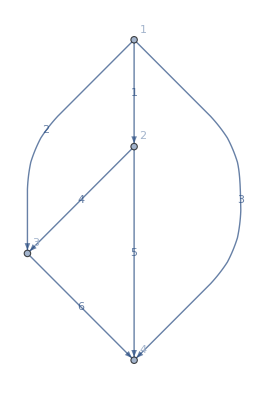

{Es1t1,Es2t2,Es3t3,Es4t4,αs1t2,αs1t3,αs1t4,αs2t3,αs2t4,αs3t4,αs1t2•αs2t3,αs1t2•αs2t4,αs1t3•αs3t4,αs2t3•αs3t4,αs1t2•αs2t3•αs3t4}

{Es1t1⊗Es1t1,Es2t2⊗Es2t2,Es3t3⊗Es3t3,Es4t4⊗Es4t4,Es1t1⊗αs1t2+αs1t2⊗Es2t2,Es1t1⊗αs1t3+αs1t3⊗Es3t3,Es1t1⊗αs1t4+αs1t4⊗Es4t4,Es2t2⊗αs2t3+αs2t3⊗Es3t3,Es2t2⊗αs2t4+αs2t4⊗Es4t4,Es3t3⊗αs3t4+αs3t4⊗Es4t4,Es1t1⊗(αs1t2•αs2t3)+αs1t2⊗αs2t3+(αs1t2•αs2t3)⊗Es3t3,Es1t1⊗(αs1t2•αs2t4)+αs1t2⊗αs2t4+(αs1t2•αs2t4)⊗Es4t4,Es1t1⊗(αs1t3•αs3t4)+αs1t3⊗αs3t4+(αs1t3•αs3t4)⊗Es4t4,Es2t2⊗(αs2t3•αs3t4)+αs2t3⊗αs3t4+(αs2t3•αs3t4)⊗Es4t4,Es1t1⊗(αs1t2•αs2t3•αs3t4)+αs1t2⊗(αs2t3•αs3t4)+(αs1t2•αs2t3)⊗αs3t4+(αs1t2•αs2t3•αs3t4)⊗Es4t4}

```mathematica
(* Instructions for generating a Path algebra *)

(* First create the quiver via its adjacency matrix *)
(* For now assume multiplicity 1 *)
PathA=AdjacencyGraph[({{0, 1, 1, 1}, {0, 0, 1, 1}, {0, 0, 0, 1}, {0, 0, 0, 0}}),DirectedEdges->True,EdgeLabels->"Index",VertexLabels->Automatic]
PArank=Length[VertexList[PathA]];

(* Next generate the set of generators from the vertex set *)

Q0=StringJoin["Es",ToString[#],"t",ToString[#]]&/@Range[PArank];
Q0=(Symbol[#])&/@Q0;
(SetNonCommutative[#])&/@Q0;

(* Next generate the set of generators from the directed edge set *)

Q1P=Table[{},{i,1,PArank},{j,1,PArank}];
For[i=1,i≤PArank,i++,
For[j=1,j≤PArank,j++,
 For[t=1,t≤AdjacencyMatrix[PathA][[i]][[j]],t++,AppendTo[Q1P[[i]][[j]],StringJoin[  FromLetterNumber[t,"Greek"], (* For a given pair of source and targets enumerate using Greek letters *)
"s",ToString[i],"t",ToString[j]]]]]];
Q1P=Flatten[Q1P,2] ;
Q1P=(Symbol[#])&/@Q1P;
(SetNonCommutative[#])&/@Q1P;

PathAgen=Union[Q0,Q1P];

(* Now define relations *)
PArelations={};
Module[{first,second},
Table[ (* run a 2D for loop over PathAgen *)
first=ToString[PathAgen[[i]]];
second=ToString[PathAgen[[j]]];
If[StringCases[first,NumberString][[2]] (* pull out the target of the path "i" *)
==StringCases[second,NumberString][[1]], (* check to see if it equals the source of the path "j" *)
If[StringTake[first,1]=="E",AppendTo[PArelations,PathAgen[[i]]**PathAgen[[j]]->PathAgen[[j]]],(* when the source and target identify, indicate the vertex "E" idempotent in the first term *)
If[StringTake[second,1]=="E",AppendTo[PArelations,PathAgen[[i]]**PathAgen[[j]]->PathAgen[[i]]], (* when the source and target identify, indicate the vertex "E" idempotent in the second term *)
Null(* The source and target overlap, but no need to indicate any relation *)]],
AppendTo[PArelations,PathAgen[[i]]**PathAgen[[j]]->0]] (* The source and target are mismatched *)
,{i,1,Length[PathAgen]},{j,1,Length[PathAgen]}]
];
PArelations=Flatten[PArelations];
(* (Print[#])&/@PArelations; *)

(* Generate its basis Modulo cycles*)
ExtendedPArelations=PArelations;
Table[ AppendTo[ExtendedPArelations,Q1P[[i]]**___**Q1P[[i]]->0];AppendTo[ExtendedPArelations,__**Q1P[[i]]**Q1P[[i]]->0];AppendTo[ExtendedPArelations,Q1P[[i]]**Q1P[[i]]**__->0],
{i,1,Length[Q1P]}];
ExtendedPArelations;
PAbasis=PathAgen;
PAbasis=FixedPoint[Complement[NCReplaceRepeated[Flatten[Table[NonCommutativeMultiply[#[[i]],PathAgen[[j]]],{i,1,Length[#]},{j,1,Length[PathAgen]}],2],ExtendedPArelations],{0}]&,PAbasis]

(* Define comultiplication for the Path Algebra *)

PADelta[a_NonCommutativeMultiply]:=If[FreeQ[Q0,a],Plus[Q0[[ToExpression[StringCases[ToString[First[a]],NumberString][[1]]]]]⊗a,Sum[Fold[#1**#2 &,1,{a[[;;i]]}]⊗Fold[NonCommutativeMultiply,1,{a[[i+1;;]]}],{i,1,Length[a]-1}],a⊗Q0[[ToExpression[StringCases[ToString[Last[a]],NumberString][[2]]]]]],a⊗a];
PADelta[a_?NonCommutativeQ]:=If[FreeQ[Q0,a],Plus[Q0[[ToExpression[StringCases[ToString[a],NumberString][[1]]]]]⊗a,a⊗Q0[[ToExpression[StringCases[ToString[a],NumberString][[2]]]]]],a⊗a];

(* Comultiplication is an algebra map *)
PADelta[a_Plus]:=(PADelta[#])&/@ a;
PADelta[a_?CommutativeQ b_]:=a PADelta[b]/;a≠1;
PADelta[a_?CommutativeQ]:=a PADelta[1]/;a≠1;
(* PADelta[a_NonCommutativeMultiply]:=(PADelta[#])& /@ a;*)

(* Comultiplication is Coassociative,
	worth looking at how order is chosen here later *)
PADelta[a_⊗b__]:=PADelta[a]⊗b;
PADelta[#]&/@PAbasis
(* Define the Conunit *)
PAEps[a_]:=If[FreeQ[Q0,a],0,1]; (* The counit is 1 on th elist of vertices, Q0, 0 otherwise *)

(* The Counit is an algebra map *)
PAEps[a_Plus]:=(PAEps[#]) & /@ a;
PAEps[a_?CommutativeQ b_]:=a PAEps[b]/;a≠1;
PAEps[a_?CommutativeQ ]:=a PAEps[1]/;a≠1;
PAEps[a_NonCommutativeMultiply]:=(PAEps[#])&/@a;
```

```mathematica
(* Set up · as an action operator *)

Unprotect[CenterDot];
     ClearAttributes[CenterDot, {OneIdentity,Flat}];

     (* Pull out commutative factors *)
     CenterDot[ b_?CommutativeQ c_, d_] :=
     b CenterDot[ c, d];
     CenterDot[a_ b_?CommutativeQ , d_] :=
     b CenterDot[ a, d];
     CenterDot[ b_?CommutativeQ, c_] :=
     b CenterDot[1, c]/;b≠1; 
     CenterDot[ a_,b_?CommutativeQ c_] :=
     b CenterDot[ a, c];
     CenterDot[ a_,b_ c_?CommutativeQ ] :=
     c CenterDot[ a, b];
     CenterDot[ a_,b_?CommutativeQ] :=
     b CenterDot[a,1]/;b≠1; 

     (* Pull out sums *)
     CenterDot[a_Plus,b__]:=(CenterDot[#,b]) &/@ a;
     CenterDot[a_,b_Plus]:=(CenterDot[a,#]) &/@ b;

     (* Distribute NonCommutative Multiplication*)
      CenterDot[a_**b_,c__]:=CenterDot[a,CenterDot[b,c]]; 

     (* Control the action on the identity *)
      CenterDot[1,a_]:=a;

Protect[CenterDot];
```

```mathematica
(* Set up the action of H on A *)

(* First define ·:H⊗A->A *)
Hgen; (* generators of H *)
Agen=PathAgen; (* generators of A *)
LActionRules=Table[1·Agen[[i]]->Agen[[i]],{i,1,Length[Agen]}];
Flatten[Table[AppendTo[LActionRules,temp=Symbol[StringJoin["laH",ToString[i],"A",ToString[j],"B",ToString[k]]];SetCommutative[temp];
Hgen[[i]]·Agen[[j]]->Sum[Times[temp,Agen[[k]]],{k,1,Length[Agen]}]],{i,1,Length[Hgen]},{j,1,Length[Agen]}],2];
(* Table[AppendTo[LActionRules,(Hgen[[i]]**Hgen[[j]])·x_->Hgen[[i]]·(Hgen[[j]]·x)],{i,1,Length[Hgen]},{j,1,Length[Hgen]}]; *)


(* Next ensure that ·( **⊗Id)=(Id⊗·)·:H⊗H⊗A->A *)
(* Then ensure that 1·a->a *)
(* Both currently accounted for in the · operator definition *)

(* h·(pq)=∑(h1·p)(h2·q) *)


(* h·1=Eps[h]1 *)
A1=Sum[Q0[[i]],{i,1,Length[Q0]}];
Flatten[Table[AppendTo[LActionRules,Hgen[[i]]·A1->Eps[Hgen[[i]]]A1],{i,1,Length[Hgen]}],2];

NCRR[(x**g)·Es1t1,LActionRules]//NCExpand
```

Es1t1 laH1A10Bk laH2A1Bk+Es2t2 laH1A10Bk laH2A1Bk+Es3t3 laH1A10Bk laH2A1Bk+Es4t4 laH1A10Bk laH2A1Bk+Es1t1 laH1A11Bk laH2A1Bk+Es2t2 laH1A11Bk laH2A1Bk+Es3t3 laH1A11Bk laH2A1Bk+Es4t4 laH1A11Bk laH2A1Bk+Es1t1 laH1A1Bk laH2A1Bk+Es2t2 laH1A1Bk laH2A1Bk+Es3t3 laH1A1Bk laH2A1Bk+Es4t4 laH1A1Bk laH2A1Bk+Es1t1 laH1A2Bk laH2A1Bk+Es2t2 laH1A2Bk laH2A1Bk+Es3t3 laH1A2Bk laH2A1Bk+Es4t4 laH1A2Bk laH2A1Bk+Es1t1 laH1A3Bk laH2A1Bk+Es2t2 laH1A3Bk laH2A1Bk+Es3t3 laH1A3Bk laH2A1Bk+Es4t4 laH1A3Bk laH2A1Bk+Es1t1 laH1A4Bk laH2A1Bk+Es2t2 laH1A4Bk laH2A1Bk+Es3t3 laH1A4Bk laH2A1Bk+Es4t4 laH1A4Bk laH2A1Bk+Es1t1 laH1A5Bk laH2A1Bk+Es2t2 laH1A5Bk laH2A1Bk+Es3t3 laH1A5Bk laH2A1Bk+Es4t4 laH1A5Bk laH2A1Bk+Es1t1 laH1A6Bk laH2A1Bk+Es2t2 laH1A6Bk laH2A1Bk+Es3t3 laH1A6Bk laH2A1Bk+Es4t4 laH1A6Bk laH2A1Bk+Es1t1 laH1A7Bk laH2A1Bk+Es2t2 laH1A7Bk laH2A1Bk+Es3t3 laH1A7Bk laH2A1Bk+Es4t4 laH1A7Bk laH2A1Bk+Es1t1 laH1A8Bk laH2A1Bk+Es2t2 laH1A8Bk laH2A1Bk+Es3t3 laH1A8Bk laH2A1Bk+Es4t4 laH1A8Bk laH2A1Bk+Es1t1 laH1A9Bk laH2A1Bk+Es2t2 laH1A9Bk laH2A1Bk+Es3t3 laH1A9Bk laH2A1Bk+Es4t4 laH1A9Bk laH2A1Bk+laH1A10Bk laH2A1Bk αs1t1+laH1A11Bk laH2A1Bk αs1t1+laH1A1Bk laH2A1Bk αs1t1+laH1A2Bk laH2A1Bk αs1t1+laH1A3Bk laH2A1Bk αs1t1+laH1A4Bk laH2A1Bk αs1t1+laH1A5Bk laH2A1Bk αs1t1+laH1A6Bk laH2A1Bk αs1t1+laH1A7Bk laH2A1Bk αs1t1+laH1A8Bk laH2A1Bk αs1t1+laH1A9Bk laH2A1Bk αs1t1+laH1A10Bk laH2A1Bk αs1t2+laH1A11Bk laH2A1Bk αs1t2+laH1A1Bk laH2A1Bk αs1t2+laH1A2Bk laH2A1Bk αs1t2+laH1A3Bk laH2A1Bk αs1t2+laH1A4Bk laH2A1Bk αs1t2+laH1A5Bk laH2A1Bk αs1t2+laH1A6Bk laH2A1Bk αs1t2+laH1A7Bk laH2A1Bk αs1t2+laH1A8Bk laH2A1Bk αs1t2+laH1A9Bk laH2A1Bk αs1t2+laH1A10Bk laH2A1Bk αs1t3+laH1A11Bk laH2A1Bk αs1t3+laH1A1Bk laH2A1Bk αs1t3+laH1A2Bk laH2A1Bk αs1t3+laH1A3Bk laH2A1Bk αs1t3+laH1A4Bk laH2A1Bk αs1t3+laH1A5Bk laH2A1Bk αs1t3+laH1A6Bk laH2A1Bk αs1t3+laH1A7Bk laH2A1Bk αs1t3+laH1A8Bk laH2A1Bk αs1t3+laH1A9Bk laH2A1Bk αs1t3+laH1A10Bk laH2A1Bk αs1t4+laH1A11Bk laH2A1Bk αs1t4+laH1A1Bk laH2A1Bk αs1t4+laH1A2Bk laH2A1Bk αs1t4+laH1A3Bk laH2A1Bk αs1t4+laH1A4Bk laH2A1Bk αs1t4+laH1A5Bk laH2A1Bk αs1t4+laH1A6Bk laH2A1Bk αs1t4+laH1A7Bk laH2A1Bk αs1t4+laH1A8Bk laH2A1Bk αs1t4+laH1A9Bk laH2A1Bk αs1t4+laH1A10Bk laH2A1Bk αs2t3+laH1A11Bk laH2A1Bk αs2t3+laH1A1Bk laH2A1Bk αs2t3+laH1A2Bk laH2A1Bk αs2t3+laH1A3Bk laH2A1Bk αs2t3+laH1A4Bk laH2A1Bk αs2t3+laH1A5Bk laH2A1Bk αs2t3+laH1A6Bk laH2A1Bk αs2t3+laH1A7Bk laH2A1Bk αs2t3+laH1A8Bk laH2A1Bk αs2t3+laH1A9Bk laH2A1Bk αs2t3+laH1A10Bk laH2A1Bk αs2t4+laH1A11Bk laH2A1Bk αs2t4+laH1A1Bk laH2A1Bk αs2t4+laH1A2Bk laH2A1Bk αs2t4+laH1A3Bk laH2A1Bk αs2t4+laH1A4Bk laH2A1Bk αs2t4+laH1A5Bk laH2A1Bk αs2t4+laH1A6Bk laH2A1Bk αs2t4+laH1A7Bk laH2A1Bk αs2t4+laH1A8Bk laH2A1Bk αs2t4+laH1A9Bk laH2A1Bk αs2t4+laH1A10Bk laH2A1Bk αs3t4+laH1A11Bk laH2A1Bk αs3t4+laH1A1Bk laH2A1Bk αs3t4+laH1A2Bk laH2A1Bk αs3t4+laH1A3Bk laH2A1Bk αs3t4+laH1A4Bk laH2A1Bk αs3t4+laH1A5Bk laH2A1Bk αs3t4+laH1A6Bk laH2A1Bk αs3t4+laH1A7Bk laH2A1Bk αs3t4+laH1A8Bk laH2A1Bk αs3t4+laH1A9Bk laH2A1Bk αs3t4

```mathematica
NCTensorMultiply[a_Plus]:=(NCTensorMultiply[#]) & /@ a;
NCTensorMultiply[a_Plus**b__]:=(NCTensorMultiply[#**b])&/@a;
NCTensorMultiply[a_**b_Plus]:=(NCTensorMultiply[a**#])&/@b;
NCTensorMultiply[a_**b_Plus**c__]:=(NCTensorMultiply[a**#**c])&/@b;
NCTensorMultiply[a_?CircleTimesQ ** b_?CircleTimesQ]:=
Inner[NonCommutativeMultiply,a,b,CircleTimes]/;Length[a]==Length[b];
NCTensorMultiply[a_?CircleTimesQ ** b_?CircleTimesQ]:=
Print["Unequal Length Tensors"]/;Length[a]≠Length[b];
NCTensorMultiply[a_?CircleTimesQ ** b_?CircleTimesQ**c___]:=
NCTensorMultiply[Inner[NonCommutativeMultiply,a,b,CircleTimes]**c]/;Length[a]==Length[b];
NCTensorMultiply[_]:=Echo["invalid input"];

Delta[g**g**g**g]//NCRR
Delta[x**g**g**g]//NCRR
Delta[g**x**g**g]//NCRR
Delta[x**x**g**g]//NCRR
Delta[g**g**x**g]//NCRR
Delta[x**g**x**g]//NCRR
Delta[g**x**x**g]//NCRR
Delta[x**x**x**g]//NCRR
Delta[g**g**g**x]//NCRR
Delta[x**g**g**x]//NCRR
Delta[g**x**g**x]//NCRR
Delta[x**x**g**x]//NCRR
Delta[g**g**x**x]//NCRR
Delta[x**g**x**x]//NCRR
Delta[g**x**x**x]//NCRR
Delta[x**x**x**x]//NCRR
Eps[g**g**g**g]//NCRR;
Eps[x**g**g**g]//NCRR;
Eps[g**x**g**g]//NCRR;
Eps[x**x**g**g]//NCRR;
Eps[g**g**x**g]//NCRR;
Eps[x**g**x**g]//NCRR;
Eps[g**x**x**g]//NCRR;
Eps[x**x**x**g]//NCRR;
Eps[g**g**g**x]//NCRR;
Eps[x**g**g**x]//NCRR;
Eps[g**x**g**x]//NCRR;
Eps[x**x**g**x]//NCRR;
Eps[g**g**x**x]//NCRR;
Eps[x**g**x**x]//NCRR;
Eps[g**x**x**x]//NCRR;
Eps[x**x**x**x]//NCRR;
S[g**g**g**g]//NCRR
S[x**g**g**g]//NCRR
S[g**x**g**g]//NCRR
S[x**x**g**g]//NCRR
S[g**g**x**g]//NCRR
S[x**g**x**g]//NCRR
S[g**x**x**g]//NCRR
S[x**x**x**g]//NCRR
S[g**g**g**x]//NCRR
S[x**g**g**x]//NCRR
S[g**x**g**x]//NCRR
S[x**x**g**x]//NCRR
S[g**g**x**x]//NCRR
S[x**g**x**x]//NCRR
S[g**x**x**x]//NCRR
S[x**x**x**x]//NCRR
```

g⊗g

1⊗x+x⊗g

ⅇ^((2 ⅈ π)/3) 1⊗x+ⅇ^((2 ⅈ π)/3) x⊗g

(g•g)⊗(x•x•g•g)+(x•g•g)⊗x+ⅇ^((2 ⅈ π)/3) (x•g•g)⊗x+(x•x•g•g)⊗g

ⅇ^(-(2 ⅈ π)/3) 1⊗x+ⅇ^(-(2 ⅈ π)/3) x⊗g

ⅇ^((2 ⅈ π)/3) (g•g)⊗(x•x•g•g)+ⅇ^(-(2 ⅈ π)/3) (x•g•g)⊗x+ⅇ^((2 ⅈ π)/3) (x•g•g)⊗x+ⅇ^((2 ⅈ π)/3) (x•x•g•g)⊗g

ⅇ^(-(2 ⅈ π)/3) (g•g)⊗(x•x•g•g)+(x•g•g)⊗x+ⅇ^(-(2 ⅈ π)/3) (x•g•g)⊗x+ⅇ^(-(2 ⅈ π)/3) (x•x•g•g)⊗g

(x•g)⊗(x•x•g•g)+ⅇ^(-(2 ⅈ π)/3) (x•g)⊗(x•x•g•g)+ⅇ^((2 ⅈ π)/3) (x•g)⊗(x•x•g•g)+(x•x•g)⊗x+ⅇ^(-(2 ⅈ π)/3) (x•x•g)⊗x+ⅇ^((2 ⅈ π)/3) (x•x•g)⊗x

1⊗x+x⊗g

ⅇ^(-(2 ⅈ π)/3) (g•g)⊗(x•x•g•g)+(x•g•g)⊗x+ⅇ^(-(2 ⅈ π)/3) (x•g•g)⊗x+ⅇ^(-(2 ⅈ π)/3) (x•x•g•g)⊗g

(g•g)⊗(x•x•g•g)+(x•g•g)⊗x+ⅇ^((2 ⅈ π)/3) (x•g•g)⊗x+(x•x•g•g)⊗g

(x•g)⊗(x•x•g•g)+ⅇ^(-(2 ⅈ π)/3) (x•g)⊗(x•x•g•g)+ⅇ^((2 ⅈ π)/3) (x•g)⊗(x•x•g•g)+(x•x•g)⊗x+ⅇ^(-(2 ⅈ π)/3) (x•x•g)⊗x+ⅇ^((2 ⅈ π)/3) (x•x•g)⊗x

ⅇ^((2 ⅈ π)/3) (g•g)⊗(x•x•g•g)+ⅇ^(-(2 ⅈ π)/3) (x•g•g)⊗x+ⅇ^((2 ⅈ π)/3) (x•g•g)⊗x+ⅇ^((2 ⅈ π)/3) (x•x•g•g)⊗g

(x•g)⊗(x•x•g•g)+ⅇ^(-(2 ⅈ π)/3) (x•g)⊗(x•x•g•g)+ⅇ^((2 ⅈ π)/3) (x•g)⊗(x•x•g•g)+(x•x•g)⊗x+ⅇ^(-(2 ⅈ π)/3) (x•x•g)⊗x+ⅇ^((2 ⅈ π)/3) (x•x•g)⊗x

(x•g)⊗(x•x•g•g)+ⅇ^(-(2 ⅈ π)/3) (x•g)⊗(x•x•g•g)+ⅇ^((2 ⅈ π)/3) (x•g)⊗(x•x•g•g)+(x•x•g)⊗x+ⅇ^(-(2 ⅈ π)/3) (x•x•g)⊗x+ⅇ^((2 ⅈ π)/3) (x•x•g)⊗x

2 (x•x)⊗(x•x•g•g)+2 ⅇ^(-(2 ⅈ π)/3) (x•x)⊗(x•x•g•g)+2 ⅇ^((2 ⅈ π)/3) (x•x)⊗(x•x•g•g)

g•g

-(x•g•g)

-ⅇ^((2 ⅈ π)/3) (x•g•g)

ⅇ^((2 ⅈ π)/3) (x•x•g•g)

-ⅇ^(-(2 ⅈ π)/3) (x•g•g)

ⅇ^(-(2 ⅈ π)/3) (x•x•g•g)

x•x•g•g

0

-(x•g•g)

x•x•g•g

ⅇ^((2 ⅈ π)/3) (x•x•g•g)

0

ⅇ^(-(2 ⅈ π)/3) (x•x•g•g)

0

0

0